## Base Model - The Simplest Model

To deepen our understanding of the system, the first step is to develop a foundational model based on the framework outlined in the paper "When Zombies Attack".

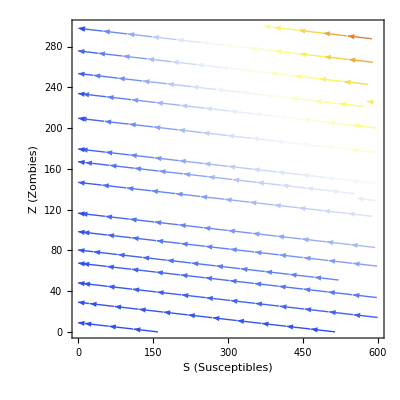

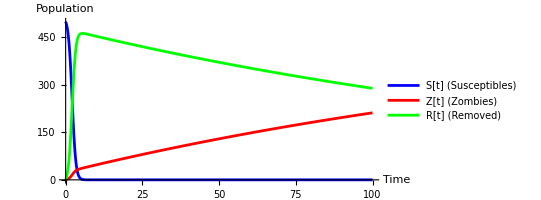

```mathematica
(*Define the Base Model*)
baseModel={
S'[t]==Π-β S[t] Z[t]-δ ,
Z'[t]==β S[t] Z[t]+ζ R[t]-α S[t] Z[t],
R'[t]==δ S[t]+α S[t] Z[t]-ζ R[t]
};

(*Define Initial Conditions& Parameters*)
initialConditions={S[0]==500,Z[0]==1,R[0]==0};
parameters={
α->5/100,(*Zombie Removal Rate*)
β->53/1000,(*Infection Rate*)
ζ->5/1000,(*Rate that the Dead Resurrect*)
δ->0,(*Susceptible Death Rate*)
Π->0 (*Susceptible Birthrate*)
};
timePeriod={t,0,100};

(*Solve Numerically*)
solution=NDSolve[Join[baseModel/. parameters,initialConditions],{S,Z,R},timePeriod];

(*Stream Plot for S[t] vs Z[t]*)
streamPlot=StreamPlot[Evaluate[{Π-β S Z-δ ,β S Z-α S Z}/. parameters],{S,0,600},{Z,0,300},StreamStyle->Arrowheads[Small],PlotRange->All,AxesLabel->{"S (Susceptibles)","Z (Zombies)"},StreamColorFunction->"TemperatureMap",StreamColorFunctionScaling->True,AspectRatio->1];
streamPlot

(*Time Series Plot for S[t],Z[t],and R[t]*)
timeSeriesPlot=Plot[Evaluate[{S[t],Z[t],R[t]}/. solution],{t,0,100},PlotStyle->{Blue,Red,Green},PlotLegends->{"S[t] (Susceptibles)","Z[t] (Zombies)","R[t] (Removed)"},AxesLabel->{"Time","Population"},PlotRange->All,AspectRatio->1/2];
timeSeriesPlot
```

### Investigating Stable point

From the stream plot, unless α is less than β and ζ, humans will lose. We can prove this by investigating its eigenvalues.

```mathematica
(*Solve for equilibrium points - Assume Π=δ=0*)
steadyState=Solve[{
-β S Z==0,
β S Z+ζ R-α S Z==0,
α S Z-ζ R==0}/. parameters,{S,Z,R}]

(*If equilibrium points are valid,proceed*)If[Length[steadyState]>0,(*Define the Jacobian*)jacobian=D[{-β S Z,β S Z+ζ R-α S Z,α S Z-ζ R},{{S,Z,R}}];
(*Loop through all equilibrium points*)Do[eqPoint=steadyState[[i]];
jacobianAtEq=jacobian/. eqPoint;
eigenvalues=Eigenvalues[jacobianAtEq/. parameters];
Print["Equilibrium Point ",i,": ",eqPoint];
Print["Jacobian Matrix at Equilibrium Point ",i,": ",MatrixForm[jacobianAtEq]];
Print["Eigenvalues at Equilibrium Point ",i,": ",eigenvalues];,{i,1,Length[steadyState]}],Print["No equilibrium points found. Adjust parameters."]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{S→0,R→0},{Z→0,R→0}}

Equilibrium Point 1: {S→0,R→0}

Jacobian Matrix at Equilibrium Point 1: (-Z β | 0 | 0
-Z α+Z β | 0 | ζ
Z α | 0 | -ζ)

Eigenvalues at Equilibrium Point 1: {-1/200,0,-(53 Z)/1000}

Equilibrium Point 2: {Z→0,R→0}

Jacobian Matrix at Equilibrium Point 2: (0 | -S β | 0
0 | -S α+S β | ζ
0 | S α | -ζ)

Eigenvalues at Equilibrium Point 2: {0,(-5+3 S-√(25+1030 S+9 S^2))/2000,(-5+3 S+√(25+1030 S+9 S^2))/2000}

Since all eigenvalues are negative, the system is marginally stable. However, it also shows that if the zombie population is 0, there is a disease-free equilibrium scenario where any external factors will easily disrupt it. Meaning, if Z >0, there will be a stable equilibrium where zombies persist - in this case killing all humans.